# Seminar of Wolfram Language programming and machine learning for physics, mathematics, and engineering at Zewail City of Science and Technology

by Akram Masoud

On November 11, 2026, I had the pleasure of delivering “Wolfram Language Programming and Machine Learning for Physics, Mathematics, and Engineering” at the Center for Fundamental Physics (CFP), Zewail City of Science and Technology. The seminar provided a welcoming setting for exploring how Wolfram Mathematica can support scientific learning and research through programming, symbolic and numerical computation, visualization, and machine learning. This abridged version of the seminar notebook presents the introductory demonstrations, applications across scientific disciplines, and a structured learning roadmap, with suggested timelines and pathways toward official Wolfram certifications. The machine learning demonstrations, including the introduction to physics-informed neural networks (PINNs), have been omitted from this version to meet the upload size limit. The complete notebook is available here. I presented the seminar as a Wolfram Certified Instructor in Mathematica, a Wolfram Student Ambassador, and an Educational Technology Engineer. Through my website, SciLearnix, I work on Mathematica programming and machine learning, scientific writing, and mathematics. I am also a PhD student in Mathematical Astronomy at the Department of Astronomy, Space Science and Meteorology, Faculty of Science, Cairo University, under the supervision of Dr. Walid Rahoma. My sincere thanks go to Dr. Tahia F. Dabash and Mr. Hussein Elkhaldy for proposing the initiative, and to Dr. Ahmed Ayad and Dr. Shaaban Khalil for organizing and hosting the seminar. I am grateful to the CFP and Zewail City for the opportunity, to Wolfram for supporting my work as a Student Ambassador, and to everyone who attended and contributed to the discussion.

## Natural Language and Built-In Knowledge

Explore natural language input and built-in knowledge to perform computations and access real-world data.

### Natural Language Input

Enter requests in plain English to perform calculations, solve equations, create plots, and explore real-world information. At the start of a new input cell, press =, then type your request.

List the integers from 1 to 10:

WolframAlphaQueryParseResults

{1,2,3,4,5,6,7,8,9,10}

Solve a system of two linear equations:

WolframAlphaQueryParseResults

{{x→3/2,y→1/2}}

Integrate a trigonometric expression:

WolframAlphaQueryParseResults

-1/2 Cos[2 x]+2 Sin[x]

Plot a function using natural language input:

WolframAlphaQueryParseResults

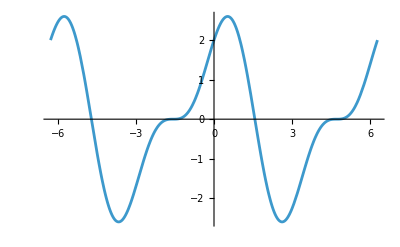

Reverse the letters in “welcome”:

WolframAlphaQueryParseResults

emoclew

Explore Egypt’s population from 1900 to 2026:

WolframAlphaQueryParseResults

TimeSeries

Request a picture of a planet:

WolframAlphaQueryParseResults

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Request an image of a water molecule:

WolframAlphaQueryParseResults

-Graphics-

Request a picture of a caffeine molecule:

WolframAlphaQueryParseResults

-Graphics3D-

### Wolfram Entities

Entities represent real-world objects, such as countries, chemicals, and species, as symbolic expressions with accessible properties. Use Ctrl + "=" to enter an entity through natural language, or write it directly in Wolfram Language.

Represent caffeine as a chemical entity:

```mathematica
Entity["Chemical","Caffeine"]
```

caffeine

List the available properties of caffeine:

```mathematica
Entity["Chemical","Caffeine"]["Properties"]
```

{acidity constant,adjacency matrix,alternate names,aromatic atom count,is aromatic,atom positions,atom count,atom diagram coordinates,atomic symbols,atom list,autoignition point,Beilstein number,black structure diagram,boiling point,bond counts,bonded atom indices,bond energies,bond lengths,bond list,bond types,CAS registry number,black carbon-hydrogen structure diagram,carbon-hydrogen structure diagram,orbital hybridization,codons,structure diagram,molar heat of combustion,critical pressure,critical temperature,dielectric constant,dipole moment,DOT hazard class,DOT numbers,drug interactions,EGEC number,electron affinity,electron count,element counts,element mass fraction,element types,entity classes,entity type list,EU number,flash point,formal charges,formatted name,formula,formula string,molar heat of fusion,Gmelin number,3-D graphics,H-bond acceptor count,H-bond donor count,Henry law constant,Hildebrand solubility parameter,Hill formula,Hill formula string,InChI identifier,ion counts,ion equivalents,isoelectric point,isomeric SMILES identifier,isomers,IUPAC name,Lewis dot structure,speed of light,pK_a,lower explosive limit,mass density,MDL number,mean free path,melting point,memberships,molar mass,molar volume,molecular mass,molecule,name,net ionic charge,NFPA fire rating,NFPA hazards,NFPA health rating,NFPA label,NFPA reactivity rating,non-hydrogen count,non-standard isotope count,non-standard isotope counts,non-standard isotope numbers,NSC number,odor threshold,odor,oxidation states,partition coefficient,pH,phase,proton affinity,proton count,PubChem compound ID,PubChem substance ID,refractive index,relative molecular mass,resistivity,rotatable bond count,RTECS classes,RTECS number,pK_a of side-chain,SMILES identifier,solubility,space filling 3-D graphics,3D molecule skeletal structure,structure graph,surface tension,tautomer count,molar thermal conductivity,topological polar surface area,upper explosive limit,van der Waals constants,vapor density,molar heat of vaporization,vapor pressure,dynamic viscosity}

Display caffeine’s molecular structure as a graph:

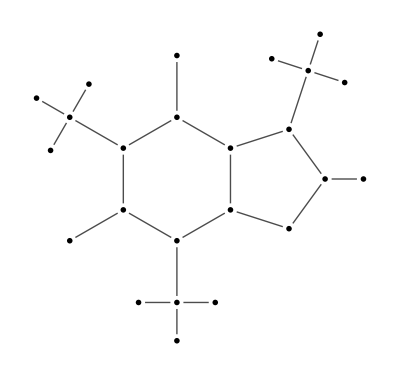

```mathematica
Entity["Chemical","Caffeine"]["StructureGraph"]
```

Display caffeine’s molecular structure:

```mathematica
Entity["Chemical","Caffeine"]["MoleculePlot"]
```

-Graphics3D-

Display caffeine’s properties and their values in a dataset:

```mathematica
Entity["Chemical","Caffeine"]["Dataset"]
```

### Wolfram|Alpha

Access Wolfram|Alpha from your notebook for computational answers and real-world information. At the start of an input cell, type ==, then enter your query.

Query Wolfram|Alpha for Egypt’s population:

population of egypt

WolframAlphaQueryResults

## Wolfram Notebook Assistant

Wolfram Notebook Assistant is an AI assistant that supports tasks ranging from answering simple coding questions and correcting errors to developing complete notebook projects from scratch through conversation. We will explore its usefulness across three tasks of increasing complexity: generating a 3D function plot, diagnosing and correcting faulty code, and creating a complete project. For each task, we will use one or more prompts, deliberately providing limited details, imperfect English, and occasional typos. We will run and review the results to assess how well the assistant meets our needs with minimal prompting effort and programming experience.

### 3D Function Plotting

In this task, you will ask the assistant to generate code for a 3D plot of sin(xy). To test how it handles informal wording and limited detail, use this prompt: “i want 3d plot of sin(xy) from -5 to 5 for both x and y. nice colours and axis names. give me the code”

Try the assistant’s first suggestion:

```mathematica
Plot3D[
  Sin[x y],
  {x,-5,5},
  {y,-5,5},
  AxesLabel->{"x","y","sin(x y)"},
  PlotLabel->"sin(x y)",
  ColorFunction->"SunsetColors",
  Mesh->None,
  PlotTheme->"Web"
]
```

-Graphics3D-

Try the assistant’s second suggestion:

```mathematica
Plot3D[
  Sin[x y],
  {x,-5,5},
  {y,-5,5},
  
]
```

-Graphics3D-

The assistant fulfilled the request despite the informal wording and grammatical errors.

### Code Debugging

In this task, you will deliberately enter faulty code intended to solve the one-dimensional wave equation for a string with fixed ends. After observing the errors, you will ask the assistant to explain and correct the code.

Enter and run the following deliberately incorrect code to solve and visualize the wave equation:

```mathematica
Clear[u,x,t,solution];
solution=NDSolveValue[{D[u[x,t],{t,2}]=D[u[x,t],{x,2}],u[x,0]==Sin[Pi x],Derivative[0,1][u][x,0]==0,u[0,t]==0,u[1,t]==0},u,{x,0,1},{t,0,2}];
Plot3D[solution[x,t],{x,0,1},{t,0,2},AxesLabel->{"Position","Time","Displacement"},ColorFunction->"SunsetColors",Mesh->None]
```

Set::write: Tag D in ∂_{t,2} u[x,t] is Protected.

NDSolveValue::deqn: Equation or list of equations expected instead of u^(2,0)[x,t] in the first argument {u^(2,0)[x,t],u[x,0]==Sin[π x],u^(0,1)[x,0]==0,u[0,t]==0,u[1,t]==0}.

NDSolveValue::dsvar: 0.0000715 cannot be used as a variable.

NDSolveValue::dsvar: 0.0715001 cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

-Graphics3D-

Now give the assistant the faulty code together with this intentionally imprecise prompt containing grammatical errors and typos: “this code not work and give errors. i want wave on a string, both ends fixed, start like sine curve and no initial speed. fix it and plot how displacement change with position and time. explain simple”.

Run the corrected code provided by the assistant:

```mathematica
Clear[u,x,t,solution];

solution=NDSolveValue[
  {
    D[u[x,t],{t,2}]==D[u[x,t],{x,2}],
    u[x,0]==Sin[Pi x],
    Derivative[0,1][u][x,0]==0,
    u[0,t]==0,
    u[1,t]==0
  },
  u,
  {x,0,1},
  {t,0,2}
];

Plot3D[
  solution[x,t],
  {x,0,1},
  {t,0,2},
  AxesLabel->{"Position","Time","Displacement"},
  ColorFunction->"SunsetColors",
  Mesh->None,
  PlotRange->All
]
```

-Graphics3D-

The assistant correctly identified the assignment operator (=) used instead of the equality operator (==), corrected the code, and explained the wave equation and its initial and boundary conditions despite the imperfect prompt.

### Complete Notebook Project

In this task, you will ask the assistant to build a complete educational notebook from scratch. The project explains a simple pendulum’s small-angle motion through mathematics, executable code, plots, and a synchronized animation. Use the following prompt:

Create and open a complete, self-contained Wolfram notebook explaining simple harmonic motion using a pendulum, suitable for high-school students. Use exactly “Pendulum SHM” as both the notebook’s title cell and window title. Define SHM as “simple harmonic motion” in the introduction. Organize the notebook into numbered sections, each with a brief explanation. Immediately before every executable input cell, include a separate descriptive caption using the actual “CodeText” cell style. Start each caption with an imperative verb and end it with a colon. Display the main equations clearly on separate lines. Include:
1. The physical system and assumptions: a point mass attached to a massless rigid support of length L, a fixed pivot, no friction or air resistance, and a small initial angle.
2. A concise mathematical explanation starting from the exact pendulum equation and deriving the small-angle equation for simple harmonic motion. Define all symbols and use radians in the equations.
3. Code that constructs and solves the approximate equation for a pendulum released from rest.
4. A plot of angular displacement against time, with labeled axes and units.
5. A smooth animation showing a fixed pivot, visible support, and bob, synchronized with a moving point on the angular displacement–time graph.
6. A short explanation of the period and its dependence on pendulum length and gravitational acceleration.

Use L=1 m, g=9.81 m/s^2, and an initial angle of 10^°, converted to radians in the code. Clearly distinguish the exact pendulum equation from its small-angle approximation. Keep the explanations, mathematics, and code concise and accessible. Initialize all variables so that all input cells can be evaluated in order from top to bottom in a fresh kernel session. Ensure that the solution is correctly evaluated as a function of time and that the animation uses the specified pendulum length. Use a consistent, readable layout throughout the notebook.

Open the assistant-generated pendulum project in Wolfram Cloud. Sign in with your Wolfram ID if required:

```mathematica
SystemOpen["https://www.wolframcloud.com/env/akram_2007_omar/Zewail%20Seminar/Pendulum%20SHM.nb"]
```

Alternatively, open the assistant-generated project embedded in this seminar notebook in a separate window:

```mathematica
NotebookPut[CurrentValue[EvaluationNotebook[],{TaggingRules,"PendulumSHM"}],WindowTitle->"Pendulum SHM"]
```

## Visualization and Interactivity

Turn equations, text, and computational results into interactive experiences. Explore oscillations with adjustable controls, uncover patterns in text, publish a web application, and visualize physical systems in motion.

### Simple Harmonic Motion

Explore how amplitude, angular frequency, and phase affect a sinusoidal function, progressing from a static plot to interactive controls.

Plot a cosine function with fixed amplitude, angular frequency, and phase:

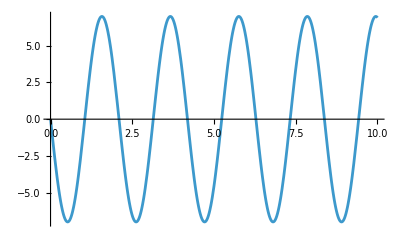

```mathematica
Plot[7 Cos[3 t+π/2],{t,0,10},PlotRange->All]
```

Vary the amplitude interactively:

```mathematica
Manipulate[Plot[a Cos[3 t+π/2],{t,-5,5},PlotRange->10],{a,1,10},ControlPlacement->Top]
```

Vary the angular frequency interactively:

```mathematica
Manipulate[Plot[7 Cos[f*t+π/2],{t,-5,5},PlotRange->All],{f,1,10},ControlPlacement->Top]
```

Vary the phase interactively:

```mathematica
Manipulate[Plot[7 Cos[3t+p],{t,-5,5},PlotRange->All],{p,0,π},ControlPlacement->Top]
```

Adjust the amplitude, angular frequency, and phase together:

```mathematica
Manipulate[Plot[a Cos[f t+p],{t,-5,5},PlotRange->10],{a,1,10},{f,1,10},{p,0,π},ControlPlacement->Top]
```

Switch between sine and cosine while adjusting the amplitude, angular frequency, and phase:

```mathematica
Manipulate[Plot[a*function[f t+p],{t,-5,5},PlotRange->10],{a,1,10},{f,1,10},{p,0,π},{function,{Sin,Cos}},ControlPlacement->Top]
```

### Text Analysis and Visualization

Explore the Wikipedia article on Mathematics through word clouds and the extraction of references to countries and nationalities.

Retrieve the text of the Wikipedia article on mathematics:

```mathematica
maths=WikipediaData["mathematics"];
```

Create a word cloud with word sizes reflecting their frequencies in the article:

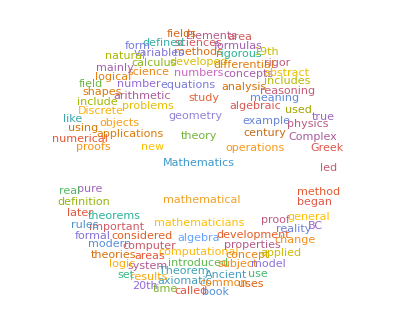

```mathematica
WordCloud[maths]
```

Extract references to countries and nationalities from the article:

```mathematica
countries=TextCases[maths,"Country"]
```

{China,Greece,Greeks,Egyptian,Egypt,Egyptian,Egypt,Egyptians,Egypt,Greek,Greeks,Greek,India,Indian,Greek,German,American,Greece,US,Greek,Greece,Greeks,Greco,Egypt,India,China,Canadian,German}

List the distinct extracted terms:

```mathematica
Union[countries]
```

{American,Canadian,China,Egypt,Egyptian,Egyptians,German,Greco,Greece,Greek,Greeks,India,Indian,US}

Create a word cloud showing the frequencies of the extracted terms:

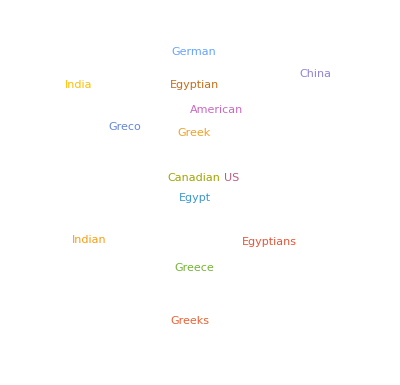

```mathematica
WordCloud[countries]
```

### Cloud Deployment

Turn a simple computation into a web form that others can access through a browser.

Find the first prime number:

```mathematica
Prime[1]
```

2

Find the tenth prime number:

```mathematica
Prime[10]
```

29

Find the thousandth prime number:

```mathematica
Prime[1000]
```

7919

Publish a web form that returns the prime number at the position entered by the user:

```mathematica
CloudPublish[FormPage[{"x"->"Integer"},If[#x>0,Prime[#x],"Enter a positive integer."]&,PageTheme->"Black"]]
```

CloudObject[https://www.wolframcloud.com/obj/037e4306-50cb-41c2-8baf-5b1308a740dc]

### Animations of Physical Systems

Explore mechanical oscillations and orbital motion through videos of a mass–spring system, Euler’s collinear solutions, Lagrange’s equilateral-triangle solutions, and a 4:3 resonant orbit in the Earth–Moon system.

Display the mass–spring system:

```mathematica
Video[Import["https://www.wolframcloud.com/obj/akram_2007_omar/Zewail%20Seminar/Mass-Spring%20System.mp4","Video"],ImageSize->600]
```

Display three examples of Euler’s three-body solutions, in which the bodies remain collinear:

```mathematica
Row[Video[Import[#,"Video"],ImageSize->270]&/@,"            "]
```

Display three examples of Lagrange’s three-body solutions, in which the bodies maintain an equilateral-triangle configuration:

```mathematica
Row[Video[Import[#,"Video"],ImageSize->270]&/@,"            "]
```

Display a 4:3 resonant orbit in the Earth–Moon system in rotating and inertial frames, with conjunction and opposition counts:

```mathematica
Video[Import["https://www.wolframcloud.com/obj/akram_2007_omar/Zewail%20Seminar/EarthMoon_43_Resonance.mp4","Video"],ImageSize->600]
```

## Applications Across Disciplines

Explore simple examples of Wolfram Language applications in geography, Earth sciences, astronomy, mathematics, and physics.

### Geography: African Countries

Explore African countries and territories through their capitals, geographic locations, and national flags.

List the countries in Africa:

```mathematica
Entity["GeographicRegion","Africa"][EntityProperty["GeographicRegion","Countries"]]
```

{Algeria,Angola,Benin,Botswana,Burkina Faso,Burundi,Cameroon,Cape Verde,Central African Republic,Chad,Comoros,Democratic Republic of the Congo,Djibouti,Egypt,Equatorial Guinea,Eritrea,Ethiopia,Gabon,Gambia,Ghana,Guinea,Guinea-Bissau,Ivory Coast,Kenya,Lesotho,Liberia,Libya,Madagascar,Malawi,Mali,Mauritania,Mauritius,Mayotte,Morocco,Mozambique,Namibia,Niger,Nigeria,Republic of the Congo,Réunion,Rwanda,Saint Helena, Ascension and Tristan da Cunha,São Tomé and Príncipe,Senegal,Seychelles,Sierra Leone,Somalia,South Africa,South Sudan,Sudan,Eswatini,Tanzania,Togo,Tunisia,Uganda,Western Sahara,Zambia,Zimbabwe}

List the capitals of African countries and territories:

```mathematica
EntityValue[Entity["GeographicRegion","Africa"][EntityProperty["GeographicRegion","Countries"]],EntityProperty["Country","CapitalCity"]]
```

{Algiers,Luanda,Porto Novo,Gaborone,Ouagadougou,Gitega,Yaoundé,Praia,Bangui,N'Djamena,Moroni,Kinshasa,Djibouti,Cairo,Malabo,Asmara,Addis Ababa,Libreville,Banjul,Accra,Conakry,Bissau,Yamoussoukro,Nairobi,Maseru,Monrovia,Tripoli,Antananarivo,Lilongwe,Bamako,Nouakchott,Port Louis,Mamoudzou,Rabat,Maputo,Windhoek,Niamey,Abuja,Brazzaville,Saint-Denis,Kigali,Jamestown,São Tomé,Dakar,Victoria,Freetown,Mogadishu,Pretoria,Juba,Khartoum,Mbabane,Dodoma,Lomé,Tunis,Kampala,al-Ayun,Lusaka,Harare}

Display African capitals on a geographic bubble chart:

```mathematica
GeoBubbleChart[Counts[EntityValue[Entity["GeographicRegion","Africa"][EntityProperty["GeographicRegion","Countries"]],EntityProperty["Country","CapitalCity"]]]]
```

-Graphics-

Create a collage of African country flags:

```mathematica
ImageCollage@EntityValue[Entity["GeographicRegion","Africa"][EntityProperty["GeographicRegion","Countries"]],EntityProperty["Country","Flag"]]
```

-Graphics-

### Earth Sciences: Mountains and Terrain

Find nearby mountains, retrieve geographic information, and visualize terrain elevation in three dimensions.

Find the three mountains nearest to your current location:

```mathematica
mounts=GeoNearest["Mountain",Here,3]
```

{Mount Sinai,Mount Catherine,Ra's Kharūf}

Display a geographic disk centered on the second mountain:

```mathematica
disk=GeoGraphics[GeoDisk[mounts[[2]]]]
```

-Graphics-

Retrieve terrain elevation data around the second mountain:

```mathematica
data=GeoElevationData[mounts[[2]],GeoRange->Quantity[0.5, "Kilometers"]]
```

QuantityArray[…]

Plot the terrain in 3D with elevation contour lines:

```mathematica
ListPlot3D[QuantityMagnitude[data],DataRange->{{-500,500},{-500,500}},BoxRatios->Automatic,MeshFunctions->{#3&},Mesh->30,PlotRange->All,AxesLabel->{"x (m)","y (m)","Elevation (m)"},ImageSize->400]
```

-Graphics3D-

Identify the country containing Mount Catherine:

```mathematica
First[Entity["Mountain","MountCatherine::f2jqh"]["Countries"]]
```

Egypt

List the available properties of Mount Catherine:

```mathematica
Entity["Mountain","MountCatherine::f2jqh"]["Properties"]
```

{administrative region,alternate names,climbing difficulty,typical climbing months,continent,coordinates,country,elevation,entity classes,entity type list,epoch,image,isolation,latitude,longitude,mountain range,name,parent peak,position,prominence,summit reached,type}

Display Mount Catherine’s properties and their values in a dataset:

```mathematica
Entity["Mountain","MountCatherine::f2jqh"]["Dataset"]
```

### Astronomy: Moon Phases

Compare the Moon’s appearance on different dates and visualize how its phase changes over time.

Display the Moon’s phase on July 22, 1983:

```mathematica
MoonPhase[DateObject[{1983,7,22},"Day"],"Icon"]
```

-Graphics-

Display today’s Moon phase:

```mathematica
MoonPhase[Today,"Icon"]
```

-Graphics-

Display the Moon’s phase 30 days from today:

```mathematica
MoonPhase[Today+Quantity[30, "Days"],"Icon"]
```

-Graphics-

Create a collage of Moon phases for the next 30 days:

```mathematica
ImageCollage@Table[MoonPhase[Today+n Quantity[, "Days"],"Icon"],{n,30}]
```

-Graphics-

### Mathematics: Traveling Salesman Problem

The Traveling Salesman Problem seeks the shortest route that visits each location once and returns to the starting point.

Retrieve the opening paragraph of the Wikipedia article on the Traveling Salesman Problem:

```mathematica
StringSplit[WikipediaData["Traveling salesman problem"],"\n"][[1]]
```

In the theory of computational complexity, the travelling salesman problem (TSP) asks the following question: "Given a list of cities and the distances between each pair of cities, what is the shortest possible route that visits each city exactly once and returns to the origin city?" It is an NP-hard problem in combinatorial optimization, important in theoretical computer science and operations research.

List Egypt’s administrative divisions:

```mathematica
states=GeoEntities[Entity["Country","Egypt"], "AdministrativeDivision"]
```

{Alexandria, Egypt,New Valley, Egypt,Aswan, Egypt,Asyut, Egypt,Beheira, Egypt,Beni Suef, Egypt,Cairo, Egypt,Dakahlia, Egypt,Damietta, Egypt,Red Sea, Egypt,Faiyum, Egypt,Qalyubia, Egypt,Gharbia, Egypt,Giza, Egypt,Ismailia, Egypt,Kafr el-Sheikh, Egypt,Luxor, Egypt,Matruh, Egypt,Minya, Egypt,Monufia, Egypt,North Sinai, Egypt,Port Said, Egypt,Qena, Egypt,Sharqia, Egypt,South Sinai, Egypt,Sohag, Egypt,Suez, Egypt}

Find the shortest tour through Egypt’s governorates and display its total distance and the governorate names in visitation order:

```mathematica
tour=FindShortestTour[states];
tour[[1]]
StringReplace[EntityValue[states[[tour[[2]]]],"Name"],", Egypt"~~EndOfString->""]
```

3614.54 km

{Alexandria,Beheira,Monufia,Gharbia,Kafr el-Sheikh,Dakahlia,Damietta,Port Said,Sharqia,Ismailia,North Sinai,South Sinai,Suez,Cairo,Qalyubia,Faiyum,Beni Suef,Minya,Asyut,Sohag,Qena,Luxor,Red Sea,Aswan,New Valley,Giza,Matruh,Alexandria}

Display the tour on a relief map with location labels:

```mathematica
GeoListPlot[states[[tour[[2]]]],Joined->True,GeoBackground->"ReliefMap",GeoLabels->True,LabelStyle->Directive[10,Italic,Black]]//Quiet
```

-Graphics-

### Physics: Electric Fields

Electric charge is a physical property of matter that produces electric forces. It can be positive or negative and is measured in coulombs (C). The electric field at a point is the electric force per unit positive test charge: E⃗=F⃗/q_Test. Here, E⃗ is the electric field in newtons per coulomb (N/C), F⃗ is the electric force on the test charge in newtons (N), and q_Test is a small positive test charge in coulombs (C). For a point charge in vacuum, the electric field is:

E⃗(r⃗)=1/(4π ε_0) q/r^2 r̂

Here, q is the source charge in coulombs (C), and ε_0 is the vacuum permittivity. The scalar r is the distance from the source charge to the observation point, measured in meters (m). The unit vector r̂=r⃗/r points in this direction, where r⃗ is the displacement vector from the source charge to the observation point and |r⃗|=r. The following plots use relative charge strengths and omit the common positive constant 1/(4π ε₀), which does not affect field direction.

Plot the electric fields of positive and negative point charges, marking the positive charge in red and the negative charge in blue:

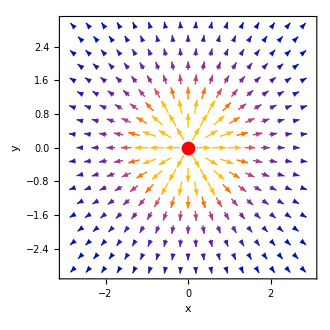
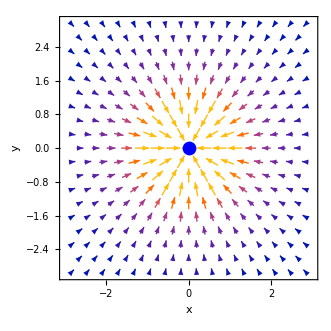

```mathematica
Row[VectorPlot[# {x,y}/((x^2+y^2)^(3/2)),{x,-3,3},{y,-3,3},]&/@{1,-1},"                 "]
```

Plot the combined electric field of a positive charge at (1,1), marked in red, and an equal-magnitude negative charge at (-1,-1), marked in blue:

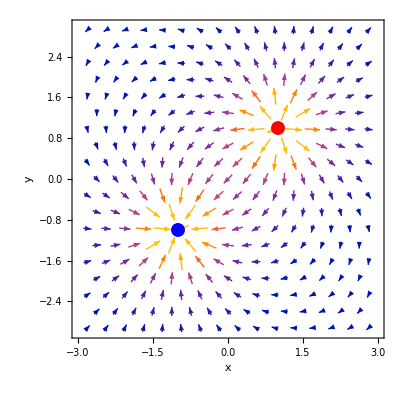

```mathematica
VectorPlot[({x,y}-{1,1})/(((x-1)^2+(y-1)^2)^(3/2))-({x,y}-{-1,-1})/(((x+1)^2+(y+1)^2)^(3/2)),{x,-3,3},{y,-3,3},]
```

Drag the locators to change the charge positions and separation, and adjust the sliders to vary their signs and strengths:

```mathematica
Manipulate[VectorPlot[(q1 ({x,y}-r1))/Norm[{x,y}-r1]^3+(q2 ({x,y}-r2))/Norm[{x,y}-r2]^3,{x,-3,3},{y,-3,3},],]
```

## Wolfram Language Roadmap

Follow a learning path from Wolfram Language fundamentals to data science, machine learning, and neural networks, supported by mathematical foundations and certification opportunities.

### Getting Mathematica

Use the following links to explore Mathematica, compare licensing options, and find access information.

Wolfram: https://www.wolfram.com/

Wolfram Language: https://www.wolfram.com/language/

Mathematica: https://www.wolfram.com/mathematica/

Mathematica Pricing: https://www.wolfram.com/mathematica/pricing/

Mathematica Personal Edition ($174/Year): https://www.wolfram.com/mathematica/pricing/personal/

Mathematica for Students ($67/Year): https://www.wolfram.com/mathematica/pricing/students/

Wolfram Egypt: https://www.wolfram.com/egypt/

### Programming Expertise

Build your programming skills through introductory resources, practical tutorials, and progressively more advanced courses.

An Elementary Introduction to Wolfram Language

-Graphics-

My recommended starting point is Stephen Wolfram’s An Elementary Introduction to the Wolfram Language, available as both a book and an interactive course. Use the book as a reference and follow the course for guided learning and hands-on practice.

Introduction to Wolfram Tech

-Graphics-

Use Introduction to Wolfram Tech to explore the capabilities of Wolfram technology and quickly review Wolfram Language fundamentals.

Hands-on Start to Wolfram Mathematica Training Tutorials

-Graphics-

Use Hands-on Start to Wolfram Mathematica Training Tutorials for a practical introduction to notebooks, calculations, graphics, and interactive presentations.

Wolfram Language Programming Proficiency

-Graphics-

I recommend the Wolfram Language Programming Proficiency series (Programming Fundamentals, Practical Programming, and Programming and Development) to strengthen your programming skills and prepare for Wolfram Language Level 1 and Level 2 certifications.

### Data Science Expertise

Develop practical data science skills through courses on data exploration, visualization, analysis, and image processing.

Multiparadigm Data Science

-Graphics-

I recommend Multiparadigm Data Science to explore an integrated workflow combining data exploration, analytical methods, automated machine learning, and interactive interfaces.

Visual Explorations in Data Science

-Graphics-

I recommend Visual Explorations in Data Science for an example-driven introduction to exploring built-in real-world data through visualization.

Image Processing

-Graphics-

I recommend Introduction to Image Processing to learn how images are represented as data and processed using classical techniques, providing a useful foundation for image-based data analysis and machine learning.

### Machine Learning Expertise

Study machine learning concepts and neural networks through books, courses, practical examples, and documentation.

Introduction to Machine Learning

-Graphics-

I recommend Introduction to Machine Learning by Etienne Bernard to build a foundation in classification, regression, clustering, dimensionality reduction, and neural networks, with examples in Wolfram Language.

Exploring AI Foundations with Wolfram Tools

-Graphics-

I recommend Exploring AI Foundations with Wolfram Tools, a three-part series covering Introduction to Machine Learning, Introduction to Neural Networks, and Wolfram Language and LLMs.

Convolutional Neural Networks for Computer Vision

-Graphics-

I recommend Convolutional Neural Networks for Computer Vision to explore network architectures, training techniques, and applications in image classification, segmentation, reconstruction, and generative modeling.

Wolfram Summer School Lecture Series

-Graphics-

The Wolfram Summer School Lecture Series offers valuable material across many topics. If your goal is to learn machine learning and neural networks, I recommend focusing on the lectures dedicated to these subjects.

Neural Networks in the Wolfram Language

I recommend Neural Networks in the Wolfram Language, a written tutorial in the Documentation Center covering network construction, training, and evaluation, with practical examples in classification, regression, computer vision, language, and audio.

Training Neural Networks with Regularization

I recommend Training Neural Networks with Regularization, a written tutorial in the Documentation Center explaining overfitting and techniques for improving generalization, including validation sets, early stopping, weight decay, and dropout.

Machine Learning and Neural Networks Guides

I recommend exploring the Machine Learning and Neural Networks guides in the Documentation Center to understand the main areas of machine learning and discover the Wolfram Language functions available for each task, from classification and regression to clustering, neural network construction, and applications involving images, text, and audio.

Elementary Neural Networks Courses

Exploring the Neural Network Framework

Introduction to Neural Networks

Neural Networks Basic Concepts

Gentle Introduction to Neural Networks

Building Blocks for Deep Learning

Applying Neural Networks

### Mathematica Mathematics

Strengthen the mathematical foundations needed for computational modeling, data science, and machine learning.

Elementary Algebra

Single Variable Calculus

Multivariable Calculus

Ordinary Differential Equations

Partial Differential Equations

Statistics

Probability Theory

Linear Algebra

Complex Analysis

Laplace Transforms

Special Functions

Finite Mathematics

Discrete Mathematics

Decision Process Theory

Game Theory

### Wolfram U and Certifications

-Graphics-

Wolfram U offers learning resources across programming, mathematics, physics, data science, AI, visualization, and modeling. Formats include interactive courses, instructor-led training, webinars, video lessons, and study groups. I particularly recommend interactive courses for self-paced learning with videos, computational notebooks, exercises, and assessments. Four types of certificates and certifications are available: Attendance, confirming participation; Completion, confirming completion of course or program requirements; Level 1 Proficiency, demonstrating competency through assessments such as timed exams; and Level 2 Applied Expertise, demonstrating practical skills through an independently assessed project. The following recommendations cover courses and certifications in programming, data science, machine learning, and mathematics, with particular attention to the mathematical foundations that support programming and machine learning.

Programming

Level 1 Proficiency: Wolfram Language, Mathematica.

Level 2 Expertise: Wolfram Language Programming.

Computational Research

Level 2 Expertise: Computational Research.

Data Science

Level 1 Proficiency: Multiparadigm Data Science, Visual Explorations in Data Science, and Image Processing.

Level 2 Expertise: Multiparadigm Data Science.

Neural Networks

Level 1 Proficiency: Neural Networks.

Level 2 Expertise: Neural Networks.

Mathematics

Level 1 Proficiency:

Statistics.

Probability Theory.

Linear Algebra.

Ordinary Differential Equations.

Partial Differential Equations.

Single Variable Calculus.

Multivariable Calculus.

Finite Mathematics.

## The Wolfram Ecosystem

Explore the Wolfram ecosystem through its core technologies, products, resources, and initiatives. Use the links below as a reference for further exploration.

Core Computational Technology

Wolfram Language: Programming and computational language.

Wolfram Engine: Executes Wolfram Language computations.

Wolfram Computational Notebooks: Interactive documents combining code, text, mathematics, and results.

WolframScript: Runs Wolfram Language from the command line.

Main Products and Platforms

Mathematica: Integrated environment for computation, research, and technical work.

Wolfram|One: Combines desktop and cloud access.

Wolfram Cloud: Online notebooks, computation, and deployment.

Wolfram|Alpha: Computational answers to natural-language questions.

Wolfram|Alpha Notebook Edition: Natural-language computation within notebooks.

Wolfram System Modeler: Modeling and simulation of physical and engineering systems.

Wolfram Player: Viewing notebooks and interacting with supported computational documents.

AI Assistance and Connections

Wolfram Notebook Assistant: AI assistance for working with Wolfram notebooks.

Wolfram|Alpha APIs: Computational knowledge services for external applications.

Repositories and Reusable Resources

Wolfram Function Repository: Additional ready-to-use functions.

Wolfram Data Repository: Data resources for computation and analysis.

Wolfram Neural Net Repository: Neural network models and examples.

Wolfram Paclet Repository: Packages extending Wolfram Language.

Wolfram Prompt Repository: Reusable prompts for language-model workflows.

Wolfram Example Repository: Computational examples and applications.

Wolfram Demonstrations Project: Interactive explorations of scientific and mathematical concepts.

Wolfram Notebook Archive: Notebooks, computational essays, and educational materials.

Wolfram Research on GitHub: Public software projects and integration tools.

Documentation and Learning

Wolfram Documentation Center: Function references, examples, tutorials, and guides.

Wolfram U: Courses, webinars, study groups, and learning activities.

Fast Introduction for Programmers: Introduction for people with programming experience.

Fast Introduction for Math Students: Introduction through mathematical ideas.

Wolfram Books: Books about Wolfram technologies and applications.

Wolfram Media: Books and publications.

Community and Scientific Communication

Wolfram Community: Share projects, ask questions, and discuss computational work.

Wolfram Blog: Applications, technical articles, and product developments.

Wolfram MathWorld: Mathematical reference resource.

Stephen Wolfram Writings: Essays on computation, science, and Wolfram technologies.

Events and Educational Programs

Wolfram Events: Conferences, webinars, and other events.

Wolfram Technology Conference: Presentations on Wolfram technologies and applications.

Wolfram Summer Research Institute: Project-based learning and research.

Wolfram Winter School: Intensive learning and project work.

Wolfram High School Summer Research Program: Research opportunities for high-school students.

Wolfram Education: Resources and programs for education.

Wolfram Student Ambassador Initiative: Student participation and outreach.

Research Initiatives

Wolfram Science: Computational exploration and A New Kind of Science.

Wolfram Physics Project: Research into fundamental physics through computational models.

Wolfram Institute: Research and collaboration in computational science.

The Wolfram Functions Site: Formulas and identities for mathematical functions.

Wolfram Research Publications: Research publications and technical work.

Accounts and Support

Wolfram Account: Products, downloads, and account management.

Wolfram Support: Installation, activation, and technical guidance.

Wolfram Contact: Contact Wolfram teams.

Products and Services Directory: Explore the broader product catalog.

## Sources and Acknowledgments

Most of the material in this notebook draws on Wolfram resources. Some explanations, code examples, and demonstrations closely follow their original sources, particularly the Wolfram Language Documentation, Etienne Bernard’s Introduction to Machine Learning, and the Introduction to Wolfram Tech course. Additional material draws on Wolfram U and other Wolfram websites and resources. I also thank Luis Medrano Navarro, Luis Martin Moreno, and Sergio G. Rodrigo for their paper, “Solving differential equations with Deep Learning: a beginner's guide,” which helped me learn the fundamentals of physics-informed neural networks (PINNs). These sources are acknowledged here and recommended for further study.

## CITE THIS NOTEBOOK

Seminar of Wolfram Language programming and machine learning for physics, mathematics, and engineering at Zewail City of Science and Technology
by Akram Masoud
Wolfram Community, STAFF PICKS, November 12, 2026
https://community.wolfram.com/t/28569